## Sample generation :

```mathematica
(* 0 Define variables*)
SetDirectory[NotebookDirectory[]];
$HistoryLength = 0;

numPoint=1000; cl=0.01; 
nameSample="Sample"<>ToString[numPoint];
nameMass="Mass"<>ToString[numPoint];

N1=5;ps=0.0;
vari=Table[Subscript[x,n],{n,0,N1-1}];
variC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
complexConjugate=Join[Thread[vari->variC],Thread[variC->vari]];
DefPoly=Total[vari^(N1)]-ps*N1*Times@@vari;
 npA=Length[vari]-1;npX=npA-1; nCor=Length[vari]; dimP=npX;
Print[DefPoly];

(* patch information *)
tuples=vari;
patches = Table[{vari[[i]]-> 1}, {i, 1, Length[vari]}];
nP=Length[patches];gnumPoint=nP*numPoint;

(* redundent coordinate information *)
redunC={1,1,1,1,1};
inhomoCors=Table[RotateRight[Delete[vari, pth],npA-redunC[[pth]]],{pth,1,Length[tuples]}];
complexConjugate=Thread[vari->variC];
CinhomoCors=inhomoCors/.complexConjugate;
Print["The redundent coordinates on every patch are "<>ToString[redunC]];
```

0.+x_0^5+x_1^5+x_2^5+x_3^5+x_4^5

The redundent coordinates on every patch are {1, 1, 1, 1, 1}

Generate points in Disk before intersection  1000

We generate global points with number {5990, 5}

We generate sample with number {5, 1000, 5}

We get sample points {5, 1000, 5}

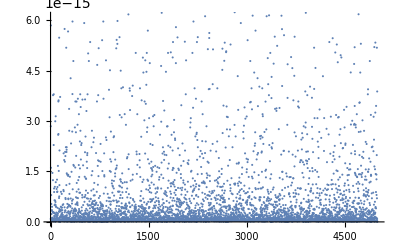

```mathematica
(* generate the uniformly distributed points on the n-sphere (norm distribution) *)
normS[m_]:=m/Norm[m];
complexifyP[m_]:=Complex@@@Partition[m,2];
ptS=complexifyP/@normS/@Transpose[Table[RandomVariate[NormalDistribution[0,1],numPoint],{i,1,nCor*2}]];
Print["Generate points in Disk before intersection  "<>ToString[Length[ptS]]];

(* generate the intersection points on the calabi-yau manifold *)
interCY[m_]:=Module[{tpoint,tDefpoly,t},tpoint=m[[1]]+t*m[[2]];
tDefpoly=DefPoly/.Thread[vari->tpoint];
tpoint/.Solve[tDefpoly==0,t]];
smallQ[m_]:=Min[Abs[m]]>cl;
gCYpts=Select[Flatten[Table[interCY[RandomChoice[ptS,2]],{i,1,Floor[gnumPoint/Length[tuples]*1.2]}],1],smallQ];
Print["We generate global points with number "<>ToString[Dimensions[gCYpts]]];

(* reform the data and make sure that every patch has the same number of data *)
pathCors[m_List]:=Module[{tm},tm=Abs[m];Position[tm,Max[tm]]];
inx=Flatten[pathCors/@gCYpts];
(*numPoint=Min[Table[Count[inx,i],{i,1,4}]];*)
lCYpts=Table[Pick[gCYpts,inx,i][[1;;numPoint]],{i,1,Length[tuples]}];
Print["We generate sample with number "<>ToString[Dimensions[lCYpts]]];
Print["We get sample points " <> ToString[Dimensions[lCYpts]]];
(*Export[ nameSample,Flatten[lCYpts,1], {"Binary", "Complex128"}];
Share[];*)

(*Check the accuracy of sample using global points*)
TestCYSample[ptCY_List]:=Abs[DefPoly/.Thread[vari->ptCY]];
Print[ListPlot[TestCYSample/@Flatten[lCYpts,1]]];
```

#### B. Project global points to local points on patches and compute the mass

We get sample points {5, 1000, 4}

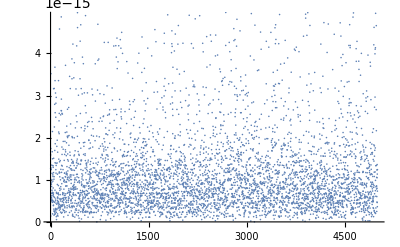

```mathematica
glob2loc[CYpoints_,redunC_]:=Module[{pth,tCYpointsl,tm,shift},
For[pth=1;tCYpointsl={},pth≤Length[tuples],pth++,
tm=CYpoints[[pth]];shift=npA-redunC[[pth]];
tCYpointsl=AppendTo[tCYpointsl,Table[RotateRight[Delete[tm[[pt]]/tm[[pt,pth]],pth],shift],{pt,1,numPoint,1}]];];
tCYpointsl
];
CYpointsl=glob2loc[lCYpts,redunC];
Print["We get sample points " <> ToString[Dimensions[CYpointsl]]];
Export[ nameSample,Flatten[CYpointsl,1], {"Binary", "Complex128"}];

(*Check the accuracy of sample using local points*)
TestCYSampleLoc[ptCY_List,pth_Integer]:=Module[{rep},
rep=Join[{vari[[pth]]->1},Thread[inhomoCors[[pth]]->ptCY]];
Abs[DefPoly/.rep]];

errs=Table[TestCYSampleLoc[CYpointsl[[pth,pt]],pth],{pth,1,Length[tuples]},{pt,1,numPoint}];
Print[ListPlot[Flatten[errs]]];
```

#### C. Mass for points on each patch:

```mathematica
gA2X[JA_,Qa_]:=Module[{tQa},
tQa=Delete[Qa/Qa[[npA]],npA];
Table[JA[[i,j]]-JA[[i,npA]]*Conjugate[tQa[[j]]]-tQa[[i]]*JA[[npA,j]]+tQa[[i]]*JA[[npA,npA]]*Conjugate[tQa[[j]]],{i,1,npX},{j,1,npX}]];

getMass[JA_,Qa_]:=N[1.0/(Det[gA2X[JA,Qa]]*Abs[Qa[[npA]]]^2)];

massG[CYpointsl_]:=Module[{K,pth,Kl,DefPolyl,JAab,Qa,HICComplex,conj,JAfunc,Qafunc,tmass,point}, 

(* Kahler potential for FS metric *)
K=Log[Total[vari*variC]];

For[pth=1;tmass={},pth≤Length[tuples],pth++,

Kl=K/.{vari[[pth]]->1,variC[[pth]]->1};
JAab=D[D[Kl,{inhomoCors[[pth]]}],{CinhomoCors[[pth]]}];
DefPolyl=DefPoly/.{vari[[pth]]->1};
Qa=D[DefPolyl,{inhomoCors[[pth]]}];

HICComplex = ( {#, _Complex} & ) /@ inhomoCors[[pth]];
conj = Thread[ CinhomoCors[[pth]] -> Conjugate[inhomoCors[[pth]] ] ];
JAfunc = Compile[Evaluate[ HICComplex ], Evaluate[ToExpression[ ToString[JAab/.conj, StandardForm]]]];
Qafunc= Compile[Evaluate[ HICComplex ], Evaluate[ToExpression[ ToString[Qa/.conj, StandardForm]]]];

tmass =AppendTo[tmass,Re[ParallelTable[point=CYpointsl[[pth,pt]];
getMass[JAfunc@@point,Qafunc@@point],{pt,1,numPoint,1}]]];
];
tmass
];
mass=massG[CYpointsl]/N[gnumPoint];
volCY=Total[Flatten[mass]];
Print[{"The volumn of X is ",volCY}];
Export[ nameMass,Flatten[mass,1], {"Binary", "Real128"}];
```

{The volumn of X is ,1.84484}

## Donaldson' s algorithm :

```mathematica
vari=Table[Subscript[x,n],{n,0,N1-1}];
variC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
npA=N1-1;npX=npA-1;nP=Length[vari]-1;
DefPoly=Total[vari^N1]-N1 ps Times@@vari;
(*Print[DefPoly];*)

(* patch information *)
patches = Table[{vari[[i]]-> 1}, {i, 1, Length[vari]}];
(* redundent coordinate information *)
redunC=ConstantArray[1,{Length[vari]}];
inhomoCors=Table[RotateRight[Delete[vari, pth],npA-redunC[[pth]]],{pth,1,Length[patches]}];
complexConjugate=Thread[vari->variC];
CinhomoCors=inhomoCors/.complexConjugate;
(*Print["The redundent coordinates on every patch are "<>ToString[redunC]];*)

(* possible symmetries *)
findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as.basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)];
α=Exp[I 2 Pi/5];
rep1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 3],Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 0]};
rep2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[x, 3]->α^3 Subscript[x, 3],Subscript[x, 4]->α^4 Subscript[x, 4]};
tvari1=vari/.rep1;tvari2=vari/.rep2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];

(*2 Read the data from files *)
getPointsFile[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
          Partition[
                 BinaryReadList[ stream, "Complex128" ], npA]];

getPointsFile2[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
      BinaryReadList[ stream, "Real128" ]];
      
indexData[numCY_List,numpp_Integer]:=Module[{tcount},tcount=0;
	Join[{0},Table[tcount+=numCY[[pth]],{pth,1,numpp-1,1}]]];
```

#### 1. Global sections & Prepare the data

```mathematica
MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum>=0,outp,{}]];

CoeffFromMonos[m_List,monos_List]:=Module[{tcoflist,ttm,i,j,zeroB},zeroB={};
For[j=1,j<=Length[m],j++,tcoflist={};
For[i=1,i<=Length[monos],i++,ttm=Coefficient[m[[j]],monos[[i]]];
AppendTo[tcoflist,ttm]];
AppendTo[zeroB,tcoflist];];
Return[zeroB]];

findInvZ5[monos_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

sAction1[p_]:=p/.rep1;
findInvZ5perm[monos_]:=Module[{},
Union[Table[Total[Union[NestList[sAction1,monos[[i]],4]]],{i,1,Length[monos]}]]];

H0Xs2[k_Integer,Monos_,cs_]:=Module[{Mt,Mt2,tk,tMonos,zeros,zeroBasis,q,qBasis},
If[k<5,Return[Monos];];tk=k-5;
(* find invariant sections *)
tMonos=findInvZ5perm[findInvZ5[MonoList[vari,tk]]];
zeros=cs*tMonos;
Print[Length[zeros]];
zeroBasis=CoeffFromMonos[zeros,Monos];
NullSpace[zeroBasis]];

(* 1 invariant basis of C on X *)
monos=findInvZ5perm[findInvZ5[MonoList[vari,k]]]; 
(*Print["The Z5*Z5 invariant global sections on A: "<>ToString[Length[monos]]];*)
(* Take the first mono as the rep of the poly *)
repMonos=Table[MonomialList[monos[[i]]][[1]],{i,1,Length[monos]}]; 
invqBasis=H0Xs2[k,repMonos,DefPoly].monos;qh0=Length[invqBasis];
Print["The Z5*Z5 invariant global sections on X: "<>ToString[qh0]];
indL=(k^3/6+5*k/6)/5;
(*Print[{"The Z5Z5 invariant global sections from index theorem for cross check: ",indL}];
*)
HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];
(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of s *)
getfuncS[pth_Integer]:=Module[{DefPolyl,qBasisl},
qBasisl = invqBasis/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[qBasisl]]];
funcS=Table[getfuncS[pth],{pth,1,Length[patches]}];

(* Find the CF of ds *)
genfuncSd[pth_Integer]:=Module[{qBasisl,dqBasisl},
qBasisl = invqBasis/.patches[[pth]];
dqBasisl=D[qBasisl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[dqBasisl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcSd=Table[genfuncSd[pth],{pth,1,Length[patches]}];

(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[funcS,funcQa,funcSd];
```

#### 2. T - operator :

```mathematica
getH[filename_String] := Module[{stream},
         stream = OpenRead[ filename, BinaryFormat -> True ];
   Partition[BinaryReadList[ stream, "Complex128" ], qh0]
        ];

getT2=Compile[{{s,_Complex,1},{H,_Complex,2}}, Module[{cs,InG,qh0,iP},
qh0=Length[s];
cs=Conjugate[s];
iP =cs.H.s;
Table[s[[A1]]*cs[[B1]], {A1, 1, qh0}, {B1, 1, qh0}]/iP
]
(*,CompilationTarget->"C"
,RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)];

Toperator[H_] := Module[{},
	ParallelEvaluate[tT=ConstantArray[0.,{qh0,qh0}];];
	lnH=Inverse[H];DistributeDefinitions[lnH];
	Table[
	DistributeDefinitions[pth];
	ParallelTable[
		point=CYpoints[[pt]];
		tT+=getT2[funcS[[pth]]@@point,lnH]*massCY[[pt]];
	,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
	Method->"CoarsestGrained",DistributedContexts->None];
,{pth,1,Length[patches]}];
N[qh0*Total[ParallelEvaluate[tT]]/volCY]];

eigenQ2[h1_,h2_] := Module[{e1,e2},
	e1=Max[Abs[Eigenvalues[h1]]];
	e2=Max[Abs[Eigenvalues[h2]]];
	Abs[(e1/e2)-1.0]];
	
iterT[Hth_Integer,Hp0_, nIter_Integer, nSaveH_Integer,nameH_,numPoint_,nameS_,nameW_]:=Module[{st,H,timeM,tH,errT},
	
	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY,qh0,npA,npX];
	DistributeDefinitions[getT2];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];
*)
	For[st =Hth;H = Hp0, st <= nIter, st++,
		timeM = SessionTime[];
		tH = Toperator[H]; 
		errT = eigenQ2[tH, H]; H=tH;
		Print[{st, errT, N[SessionTime[] - timeM]}];
		If[Mod[st,nSaveH]==0,Export[ nameH<>ToString[st], H , {"Binary", "Complex128"}]];
	];
];
```

#### 3. Evaluate the Error

```mathematica
dA2X[m_,Qa_]:=Table[m[[i]]-(Qa[[i]]/Qa[[npA]])*m[[npA]],{i,1,npX,1}];

getM2[Qa_,gs_,ds_,H_]:=Module[{cgs,dgs,cdgs,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,gij},
(* H: 1st is anti; 2nd is homo *)
cgs=Conjugate[gs];  
dgs=Transpose[Table[dA2X[ds[[i]],Qa],{i,1,qh0}]]; 
cdgs=Conjugate[dgs];

InG=cgs.H.gs;
dG=Table[cgs.H.dgs[[a]],{a,1,npX}];
cdG=Table[cdgs[[b]].H.gs,{b,1,npX}];
ddG=Table[cdgs[[b]].H.dgs[[a]],{a,1,npX},{b,1,npX}];
Mb=Table[cdG[[b]]*dG[[a]]/InG,{a,1,npX},{b,1,npX}];
gij=N[(ddG-Mb)/InG/k];
gij
];

getNmetric[H_] :=Module[ {pth,pt,tnmetric,nmetric,point,data,tJw,time},

(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[dA2X,getM2];
(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)

nmetric={};

For[pth=1,pth<=Length[patches],pth++,

DistributeDefinitions[pth];
timeM=SessionTime[];
tnmetric=ParallelTable[
		point=CYpoints[[pt]];
		getM2[funcQa[[pth]]@@point,funcS[[pth]]@@point,funcSd[[pth]]@@point,H]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];

nmetric=Join[nmetric,tnmetric];
Print[{pth,{MaxMemoryUsed[]*1024.^-3,ParallelEvaluate[MaxMemoryUsed[]*1024.^-3][[1]]},N[SessionTime[]-timeM]}];
]; nmetric];

getError[lnH_,nameMetric_,numPoint_,nameS_,nameW_]:=Module[{gij,tvolCY,tQa,tv,volK,error},

	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY,qh0,npA,npX];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
	
gij=getNmetric[lnH];
(*Print[Dimensions[gij]];*)
Export[nameMetric,  gij, {"Binary", "Complex128"}];
(*Print["Metric is saved into file"];*)

(* Compute the error from metric *)
tvolCY=Flatten[Table[tQa=funcQa[[pth]]@@CYpoints[[pt]];
Abs[tQa[[npA]]]^2,
{pth,1,Length[patches]},{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1}]];

tv = (Det/@gij)*tvolCY; 

volK = Total[tv*massCY];
error=Sum[Abs[1.0-tv[[pt]]/volK*volCY]*massCY[[pt]],{pt,1,gnumPoint}]/volCY;
error];
```

## Generalized Donaldson' s algorithm :

#### 0. Manifold & Bundle :

```mathematica
vari=Table[Subscript[x,n],{n,0,N1-1}];
variC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
npA=N1-1;npX=npA-1;nP=Length[vari]-1;
DefPoly=Total[vari^N1]-N1 ps Times@@vari;
(*Print[DefPoly];*)

(* patch information *)
patches = Table[{vari[[i]]-> 1}, {i, 1, Length[vari]}];
(* redundent coordinate information *)
redunC=ConstantArray[1,{Length[vari]}];
inhomoCors=Table[RotateRight[Delete[vari, pth],npA-redunC[[pth]]],{pth,1,Length[patches]}];
complexConjugate=Thread[vari->variC];
CinhomoCors=inhomoCors/.complexConjugate;
(*Print["The redundent coordinates on every patch are "<>ToString[redunC]];*)

(*2 Read the data from files *)
getPointsFile[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
          Partition[
                 BinaryReadList[ stream, "Complex128" ], npA]];

getPointsFile2[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
      BinaryReadList[ stream, "Real128" ]];
      
indexData[numCY_List,numpp_Integer]:=Module[{tcount},tcount=0;
	Join[{0},Table[tcount+=numCY[[pth]],{pth,1,numpp-1,1}]]];

rank=5; numF=5;
tA=1;ktA=tA+k;  
Print[{"The bundle A is ",{tA}}];
(*Print[{"The twisted bundle A is ",{ktA}}];*)

(* symmetries on manifold *)
findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as.basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)
];
α=Exp[I 2 Pi/5];
Asym1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 3],Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 0]};
Asym2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[x, 3]->α^3 Subscript[x, 3],Subscript[x, 4]->α^4 Subscript[x, 4]};
tvari1=vari/.Asym1;tvari2=vari/.Asym2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];
(*Print[MatrixForm[sym1]];
Print[MatrixForm[sym2]];*)

(* The frame information *)
tframe=Table[Subscript[e, i],{i,0,rank-1}];
subframe=Thread[tframe->IdentityMatrix[numF]];

(* The non-trivial bundle morphism *)
bmorphism1 = sym1; 
bmorphism2 = DiagonalMatrix[{1,α^4,α^3,α^2,α^1}];
ABm1=Thread[tframe->bmorphism1.tframe];
ABm2=Thread[tframe->bmorphism2.tframe];

(* Check two reps commute *)
rep1=Join[Asym1,ABm1];
rep2=Join[Asym2,ABm2];
Rep1=TensorProduct[bmorphism1,sym1]//ArrayFlatten;
Rep2=TensorProduct[bmorphism2,sym2]//ArrayFlatten;
(*Print[Total[Flatten[Abs[N[Rep1.Rep2]-N[Rep2.Rep1]]]]];*)
```

#### 1. Global Section & Data :

```mathematica
MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum>=0,outp,{}]];

CoeffFromMonos[m_List,monos_List]:=Module[{tcoflist,ttm,i,j,zeroB},zeroB={};
For[j=1,j<=Length[m],j++,tcoflist={};
For[i=1,i<=Length[monos],i++,ttm=Coefficient[m[[j]],monos[[i]]];
AppendTo[tcoflist,ttm]];
AppendTo[zeroB,tcoflist];];
Return[zeroB]];

findInvZ5[monos_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

sAction1[p_]:=p/.rep1;
findInvZ5perm[monos_]:=Module[{},
Union[Table[Total[Union[NestList[sAction1,monos[[i]],4]]],{i,1,Length[monos]}]]];

H0Xs2[k_Integer,Monos_,cs_]:=Module[{Mt,Mt2,tk,tMonos,zeros,zeroBasis,q,qBasis},
If[k<5,Return[IdentityMatrix[Length[Monos]]];];tk=k-5;
(* find invariant sections *)
tMonos=findInvZ5perm[findInvZ5[secFrame[tk]]];
(* find zero sections *)
zeros=cs*tMonos;
zeroBasis=CoeffFromMonos[zeros,Monos]; 
NullSpace[zeroBasis]];

secFrame[ktA_]:=Flatten[Outer[Times,MonoList[vari,ktA], tframe]];

(* 1 invariant basis of O(1)^5 on A *)
tmonos=secFrame[ktA];
monos=findInvZ5perm[findInvZ5[tmonos]];
(*Print["The Z5*Z5 invariant global sections of O(1\!\(\*SuperscriptBox[\()\), \(5\)]\) on A: "<>ToString[Length[monos]]];*)
repMonos=Table[MonomialList[monos[[i]]][[1]],{i,1,Length[monos]}]; 

(* Take the first mono as the rep of the poly *)
(* Each poly is an orbit for the permutation Z5 and Two polys do not intersect *)
quotientBasis=H0Xs2[ktA,repMonos,DefPoly];
invqBasis=quotientBasis.monos;qh0=Length[invqBasis];
Print["The Z5*Z5 invariant global sections of O(1\!\(\*SuperscriptBox[\()\), \(5\)]\) on X: "<>ToString[qh0]];

HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];

(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of s *)
getfuncSb[pth_Integer]:=Module[{DefPolyl,qBasisl},
qBasisl = monos/.subframe/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[qBasisl]]];
funcSb=Table[getfuncSb[pth],{pth,1,Length[patches]}];

(* Find the CF of ds *)
(* index structure
1st  (# of section)
2rd  (# of frame)
3rd  (# of derivative)
*)
genfuncSbd[pth_Integer]:=Module[{qBasisl,dqBasisl},
qBasisl = monos/.subframe/.patches[[pth]];
dqBasisl=D[qBasisl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[dqBasisl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcSbd=Table[genfuncSbd[pth],{pth,1,Length[patches]}];

(*Print["comm_shared_data"];time=SessionTime[];*)
DistributeDefinitions[npA,npX,subframe,rank,numF];
DistributeDefinitions[funcQa,funcSb,funcSbd,qh0,quotientBasis];
(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
```

#### 2. T - operator :

```mathematica
getH[filename_String] := Module[{stream},
         stream = OpenRead[ filename, BinaryFormat -> True ];
   Partition[BinaryReadList[ stream, "Complex128" ], qh0]
        ];

eigenQ2[h1_,h2_] := Module[{e1,e2},
e1=Max[Abs[Eigenvalues[h1]]];
e2=Max[Abs[Eigenvalues[h2]]];
{e1,e2,Abs[(e1/e2)-1.0]}];

getTB[s_, H_] := Module[{cs,InG,T},
cs=Conjugate[s];
(*InG=Check[Inverse[Transpose[cs].H.s],Print["error "<>ToString[pt]]];*)
(*Print[Transpose[cs].H.s];*)
InG=Inverse[Transpose[cs].H.s];
(*Print[InG];*)
T=s.InG.Transpose[cs]];

ToperatorB[H_] := Module[{pth,  pt,T,constrP,subConstr,PqGS, Sfunc,nRedun,varil,HICComplex,tpoint,point},

	ParallelEvaluate[tT=ConstantArray[0.,{qh0,qh0}];];
	lnH=Inverse[H];DistributeDefinitions[lnH];
	Table[
		DistributeDefinitions[pth];
		ParallelTable[ 
			point=CYpoints[[pt]];  
			Spt=quotientBasis.funcSb[[pth]]@@point;
			tT+=getTB[Spt,lnH]*massCY[[pt]];
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
	,{pth,1,Length[patches]}
	];
N[qh0*Total[ParallelEvaluate[tT]]/volCY/rank]
];

iterTB[Hth_Integer,Hp0_, nIter_Integer, nSaveH_Integer,nameH_,numPoint_,nameS_,nameW_]:=Module[{st,H,timeM,tH,errT},
	
	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY];
	DistributeDefinitions[getTB];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
	
	For[st =Hth;H = Hp0, st <= nIter, st++,
		timeM = SessionTime[];
		tH = ToperatorB[H]; 
		errT = eigenQ2[tH, H]; H=tH;
		Print[{st, errT, N[SessionTime[] - timeM]}];
		If[Mod[st,nSaveH]==0,Export[ nameH<>ToString[st], H , {"Binary", "Complex128"}]];
	];
	(* Test the hermitian property *)
	(*Print[Total[Flatten[H-Transpose[Conjugate[H]]]]];*)
];
```

#### 3. Evaluate Error :

```mathematica
(* Read the metric! *)
getMetricFile[filename_String] := Module[{stream},
      stream = OpenRead[ filename, BinaryFormat -> True ];
       Partition[Partition[
            BinaryReadList[ stream, "Complex128" ], 
      npX],npX]  ];

getV3[s_,ds_,lNmetric_,H_]:=Module[{cs,cds,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,tr,eign},
(* H: 1st is anti; 2nd is homo *)
cs=Conjugate[s];  cds=Conjugate[ds];

InG=Inverse[Transpose[cs].H.s];
dG=Table[Transpose[cs].H.ds[[a]],{a,1,npX}];
cdG=Table[Transpose[cds[[b]]].H.s,{b,1,npX}];
ddG=Sum[lNmetric[[b,a]]*Transpose[cds[[b]]].H.ds[[a]],{a,1,npX},{b,1,npX}];

Mb=Sum[lNmetric[[b,a]]*cdG[[b]].InG.dG[[a]],{a,1,npX},{b,1,npX}];
tM=InG.(ddG-Mb);
M=N[tM-Tr[tM]*IdentityMatrix[rank]/rank];
N[Total[Abs/@Eigenvalues[M]]]
];

getErrorB[H_,TNmetric_,numPoint_,nameS_,nameW_] := Module[{pth,pt,error,point},

	CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
	massCY =Re[getPointsFile2[nameW]];
	volCY=Total[massCY]; 
	numCY = If[numPoint==0,IntegerPart[Re[getPointsFile2[nameN]]],ConstantArray[numPoint,Length[patches]]];
	count=indexData[numCY,Length[patches]];
	Print["2a) We get sample "<>ToString[gnumPoint]];
	Print[numCY];
	Print[{"The volumn is ",volCY}];
	
	(*Print["comm_shared_data"];time=SessionTime[];*)
	DistributeDefinitions[CYpoints,massCY,count,numCY];
	DistributeDefinitions[getV3];
	(*Print[{"comm_data_done!",N[SessionTime[]-time]}];*)
	
For[pth=1;error=0.0,pth<=Length[patches],pth++,
DistributeDefinitions[pth];
timeM=SessionTime[];
error+=ParallelSum[
point=CYpoints[[pt]];  
(* Find the S *)
Spt=quotientBasis.funcSb[[pth]]@@point;
(* Find the dS *)
Qpt=funcQa[[pth]]@@point; 
tDSpt=Transpose[quotientBasis.funcSbd[[pth]]@@point,{3,2,1}];
DSpt=Transpose[Table[tDSpt[[i]]-(Qpt[[i]]/Qpt[[npA]])*tDSpt[[npA]],{i,1,npX,1}],{1,3,2}];

getV3[Spt,DSpt,TNmetric[[pt]],H]*massCY[[pt]]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
Print[{pth,{MaxMemoryUsed[]*1024.^-3,ParallelEvaluate[MaxMemoryUsed[]*1024.^-3][[1]]},N[SessionTime[]-timeM]}];
];
N[error]/volCY/rank
];
```